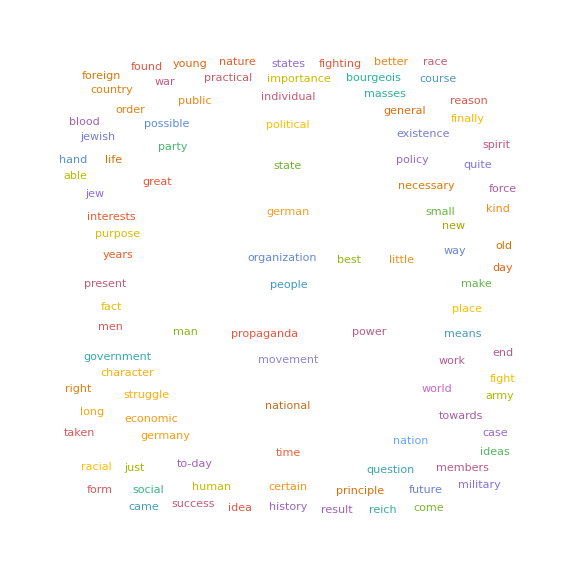
-Graphics-Mein Kampf

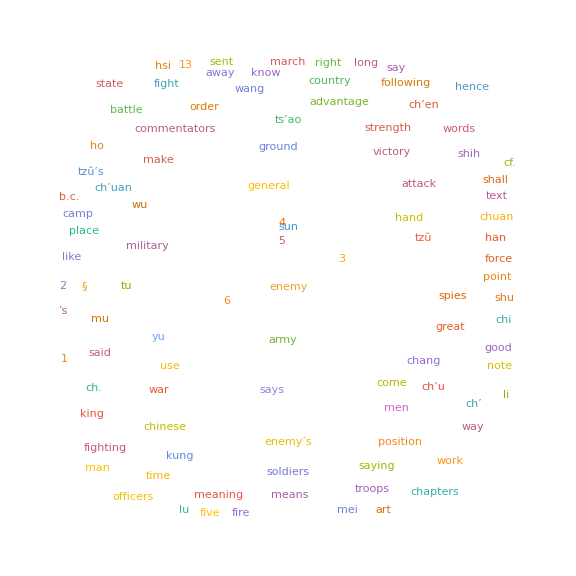
-Graphics-The Art of War

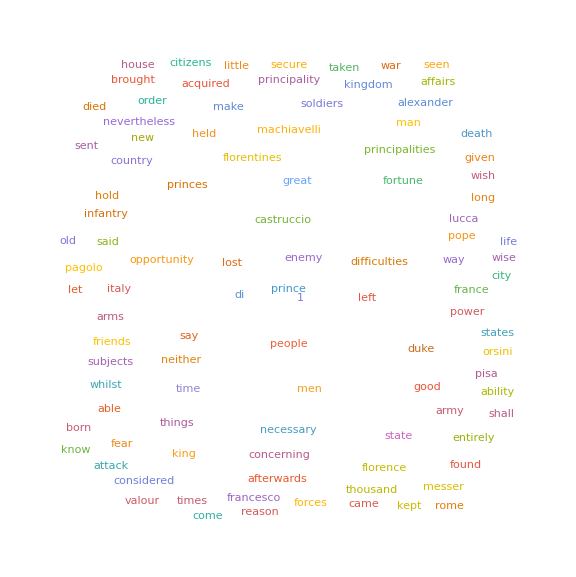
-Graphics-The Prince

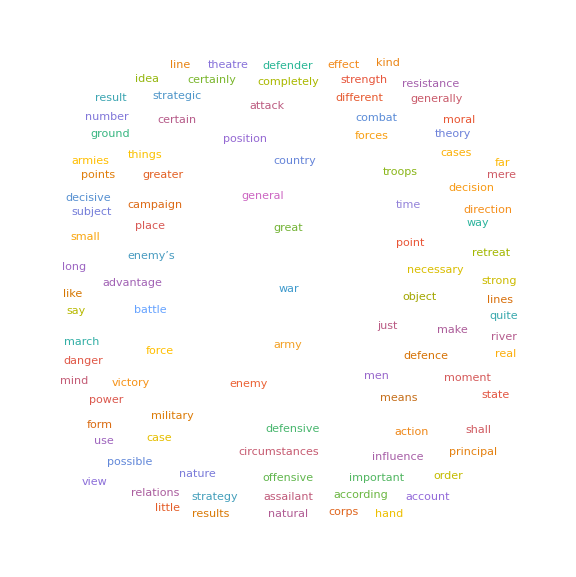
-Graphics-On War

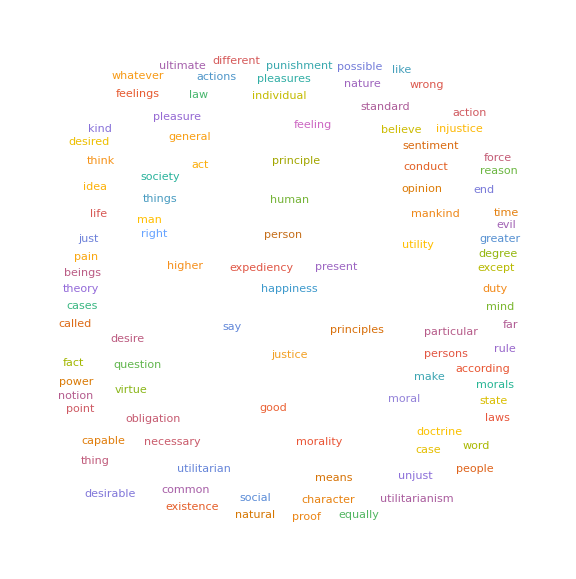
-Graphics-Utilitarianism

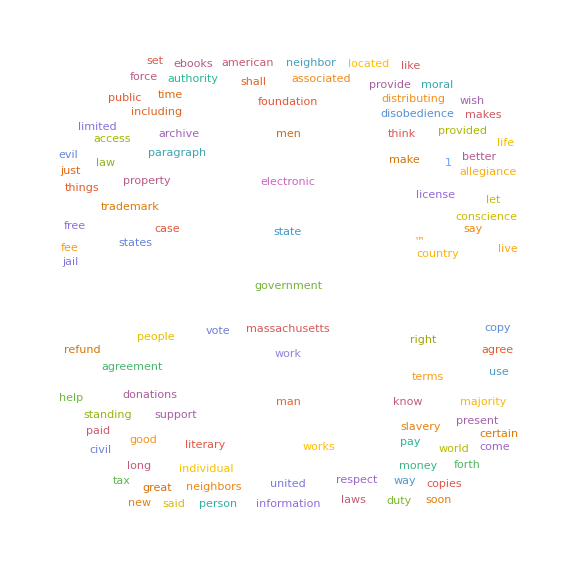
-Graphics-Civil Disobedience

-Graphics-

$Aborted

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

```mathematica
(*Import all six texts*)textList={Import["/Downloads/mein_kampf.txt","Text"],Import["/Downloads/art_of_war.txt","Text"],Import["/Downloads/the_prince.txt","Text"],Import["/Downloads/on_war.txt","Text"],Import["/Downloads/utilitarianism.txt","Text"],Import["/Downloads/civil_disobedience.txt","Text"]};

titles={"Mein Kampf","The Art of War","The Prince","On War","Utilitarianism","Civil Disobedience"};

(*Preprocess and remove stopwords*)
customStopwords={"project","gutenberg","ebook","www","http","copyright","digitized","title","chapter","book","page"};

cleanWords[text_]:=DeleteCases[DeleteStopwords[ToLowerCase[TextWords[text]]],Alternatives@@customStopwords];

Quiet[wordLists=cleanWords/@textList;];
(*Sequential labeled WordClouds*)
Do[Print[Labeled[WordCloud[wordLists[[i]],ImageSize->Large],Style[titles[[i]],Bold,14],Top]],{i,Length[wordLists]}]
(**)

(*Word frequency vectors from earlier steps*)wordFreqs=WordCounts/@textList;
commonVocab=Union@@(Keys/@wordFreqs);
vectors=Table[Lookup[wordFreqs[[i]],commonVocab,0],{i,Length[wordFreqs]}];
normVectors=Normalize/@vectors;

(*PCA embedding*)
embedPCA=DimensionReduce[normVectors,2,Method->"PrincipalComponentsAnalysis"];

pcaPlot=ListPlot[Callout@@@Transpose[{embedPCA,titles}],PlotStyle->PointSize[Large],AxesLabel->{"PCA-1","PCA-2"},PlotLabel->"Document Embedding via PCA",PlotTheme->"Detailed"];

(*UMAP embedding*)
embedUMAP=DimensionReduce[normVectors,2,Method->"UMAP"];

umapPlot=ListPlot[Callout@@@Transpose[{embedUMAP,titles}],PlotStyle->PointSize[Large],AxesLabel->{"UMAP-1","UMAP-2"},PlotLabel->"Document Embedding via UMAP",PlotTheme->"Detailed"];

(*Display plots in sequence*)
Column[{pcaPlot,umapPlot}]
{components,explained}=PrincipalComponents[normVectors,Method->"Correlation"];
components[[All,1]]
```